```mathematica
description="El -> Ga El, QED, F2(0) form factor, 1-loop";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

## Generate all desired 1-Loop diagrams using FeynArts

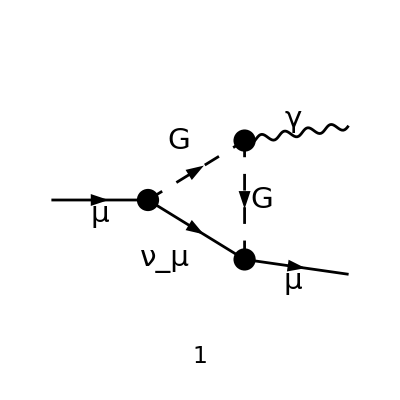

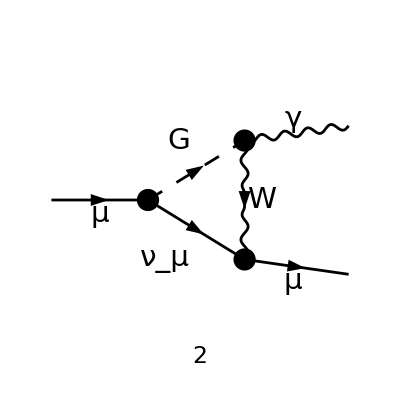

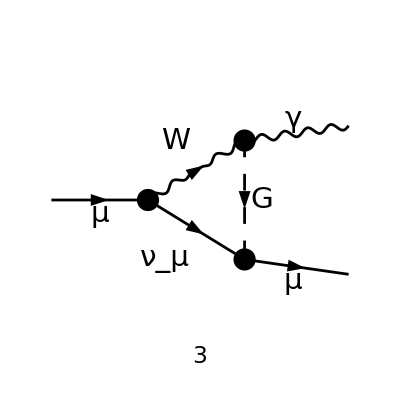

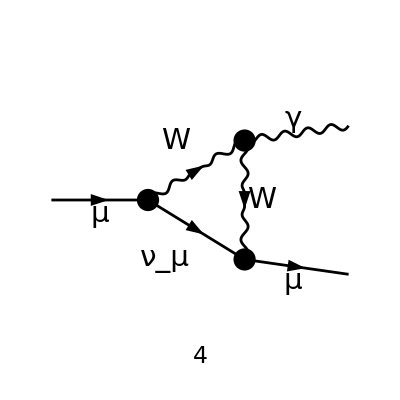

```mathematica
MakeBoxes[mu,TraditionalForm]:="μ";
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
diags=InsertFields[CreateTopologies[1,1->2,ExcludeTopologies->{Tadpoles,WFCorrections}],{F[2,{2}]}->{V[1],F[2,{2}]},InsertionLevel->{Classes},ExcludeParticles->{S[1],S[2],V[1],V[2]}];
(*diagsCT=InsertFields[CreateCTTopologies[1,1->2,ExcludeTopologies->{Tadpoles,WFCorrections}],{F[2,{1}]}->{V[1],F[2,{1}]},InsertionLevel->{Particles},ExcludeParticles->{S[1],S[2],V[1],V[2]}];*)

Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
(*Paint[diagsCT,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];*)
```

## Convert FeynArts amplitude to FeynCalc

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->1, GaugeRules->{}],IncomingMomenta->{p1},OutgoingMomenta->{k,p2},LorentzIndexNames->{mu},LoopMomenta->{q},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{SMP["e"]->-SMP["e"]}]/. k->p1-p2/. q->q+p1
```

-(φ(p_2,m_μ)).(-(ⅈ γ^Lor5.(γ̄)^7 e)/(√2 (sin(θ_W)))).(-(γ·q)).(-(ⅈ γ^Lor2.(γ̄)^7 e)/(√2 (sin(θ_W)))).(φ(p_1,m_μ)) (-((1-ξ_W)^2 (p_1+q)^Lor2 (p_1+q)^Lor3 (-p_2-q)^Lor4 (p_2+q)^Lor5)/(((p_1+q)^2-m_W^2).((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2)-((1-ξ_W) (p_1+q)^Lor2 (p_1+q)^Lor3 g^Lor4Lor5)/(((p_1+q)^2-m_W^2).((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-m_W^2).q^2)+((1-ξ_W) g^Lor2Lor3 (-p_2-q)^Lor4 (p_2+q)^Lor5)/(((p_1+q)^2-m_W^2).((p_2+q)^2-m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2)+(g^Lor2Lor3 g^Lor4Lor5)/(((p_1+q)^2-m_W^2).((p_2+q)^2-m_W^2).q^2)) ((-p_1+2 p_2+q)^Lor3 g^Lor4μ+g^Lor3μ (2 p_1-p_2+q)^Lor4+g^Lor3Lor4 (-p_1-p_2-2 q)^μ) (ε^*)^μ(p_1-p_2) e-((φ(p_2,m_μ)).(ⅈ (γ̄)^7 e m_μ)/(√2 m_W (sin(θ_W))).(-(γ·q)).(ⅈ (γ̄)^6 e m_μ)/(√2 m_W (sin(θ_W))).(φ(p_1,m_μ)) (p_1+p_2+2 q)^μ (ε^*)^μ(p_1-p_2) e)/(((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2)-(φ(p_2,m_μ)).(ⅈ (γ̄)^7 e m_μ)/(√2 m_W (sin(θ_W))).(-(γ·q)).(-(ⅈ γ^Lor2.(γ̄)^7 e)/(√2 (sin(θ_W)))).(φ(p_1,m_μ)) g^Lor3μ (g^Lor2Lor3/(((p_1+q)^2-m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2)-((1-ξ_W) (p_1+q)^Lor2 (p_1+q)^Lor3)/(((p_1+q)^2-m_W^2).((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2)) (ε^*)^μ(p_1-p_2) m_W e-(φ(p_2,m_μ)).(-(ⅈ γ^Lor3.(γ̄)^7 e)/(√2 (sin(θ_W)))).(-(γ·q)).(ⅈ (γ̄)^6 e m_μ)/(√2 m_W (sin(θ_W))).(φ(p_1,m_μ)) g^Lor2μ (g^Lor2Lor3/(((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-m_W^2).q^2)+((1-ξ_W) (-p_2-q)^Lor2 (p_2+q)^Lor3)/(((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2)) (ε^*)^μ(p_1-p_2) m_W e

## Fix the kinematics

```mathematica
FCClearScalarProducts[];
ME=SMP["m_mu"];
ScalarProduct[p1,p1]=ME^2;
ScalarProduct[p2,p2]=ME^2;
ScalarProduct[k,k]=0;
ScalarProduct[p1,p2]=ME^2;
```

## Amputate the photon polarisation

```mathematica
amp[1]=amp[0]//ReplaceAll[#,Pair[Momentum[Polarization[___],___],___]:>1]&//Contract//ReplaceAll[#,SMP["e"]^3->4 Pi SMP["e"] SMP["alpha_fs"]]&
```

(2 π (φ(p_2,m_μ)).(γ·(p_2+q)).(γ̄)^7.(γ·q).(γ·(p_1+q)).(γ̄)^7.(φ(p_1,m_μ)) (1-ξ_W)^2 (p_1+q)^μ α e (-m_μ^2-2 (p_1·q)-q^2))/(((p_1+q)^2-m_W^2).((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2 (sin(θ_W))^2)+(2 π (φ(p_2,m_μ)).(γ·(p_2+q)).(γ̄)^7.(γ·q).(γ·(p_1+q)).(γ̄)^7.(φ(p_1,m_μ)) (1-ξ_W)^2 (-p_1-p_2-2 q)^μ α e (-m_μ^2-p_1·q-p_2·q-q^2))/(((p_1+q)^2-m_W^2).((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2 (sin(θ_W))^2)+(2 π (φ(p_2,m_μ)).(γ·(p_2+q)).(γ̄)^7.(γ·q).(γ·(p_1+q)).(γ̄)^7.(φ(p_1,m_μ)) (1-ξ_W)^2 (-p_2-q)^μ α e (m_μ^2+2 (p_2·q)+q^2))/(((p_1+q)^2-m_W^2).((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2 (sin(θ_W))^2)+(2 π (φ(p_2,m_μ)).(γ·(p_1+q)).(γ̄)^7.(γ·q).(γ·(p_1+q)).(γ̄)^7.(φ(p_1,m_μ)) (1-ξ_W) (-p_1-p_2-2 q)^μ α e)/(((p_1+q)^2-m_W^2).((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-m_W^2).q^2 (sin(θ_W))^2)-(2 π (φ(p_2,m_μ)).(γ·(p_2+q)).(γ̄)^7.(γ·q).(γ·(-p_2-q)).(γ̄)^7.(φ(p_1,m_μ)) (1-ξ_W) (-p_1-p_2-2 q)^μ α e)/(((p_1+q)^2-m_W^2).((p_2+q)^2-m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2 (sin(θ_W))^2)-(2 π (φ(p_2,m_μ)).(γ·(p_2+q)).(γ̄)^7.(γ·q).(γ·(-p_1+2 p_2+q)).(γ̄)^7.(φ(p_1,m_μ)) (1-ξ_W) (-p_2-q)^μ α e)/(((p_1+q)^2-m_W^2).((p_2+q)^2-m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2 (sin(θ_W))^2)+(2 π (φ(p_2,m_μ)).(γ·(2 p_1-p_2+q)).(γ̄)^7.(γ·q).(γ·(p_1+q)).(γ̄)^7.(φ(p_1,m_μ)) (1-ξ_W) (p_1+q)^μ α e)/(((p_1+q)^2-m_W^2).((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-m_W^2).q^2 (sin(θ_W))^2)+(2 π (φ(p_2,m_μ)).(γ·(p_2+q)).(γ̄)^7.(γ·q).(γ̄)^6.(φ(p_1,m_μ)) (1-ξ_W) (-p_2-q)^μ α e m_μ)/(((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2 (sin(θ_W))^2)-(2 π (φ(p_2,m_μ)).(γ̄)^7.(γ·q).(γ·(p_1+q)).(γ̄)^7.(φ(p_1,m_μ)) (1-ξ_W) (p_1+q)^μ α e m_μ)/(((p_1+q)^2-m_W^2).((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2 (sin(θ_W))^2)-(2 π (φ(p_2,m_μ)).(γ·(p_2+q)).(γ̄)^7.(γ·q).γ^μ.(γ̄)^7.(φ(p_1,m_μ)) (1-ξ_W) α e (-m_μ^2-2 (p_1·q)-q^2))/(((p_1+q)^2-m_W^2).((p_2+q)^2-m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2 (sin(θ_W))^2)+(2 π (φ(p_2,m_μ)).γ^μ.(γ̄)^7.(γ·q).(γ·(p_1+q)).(γ̄)^7.(φ(p_1,m_μ)) (1-ξ_W) α e (m_μ^2+2 (p_2·q)+q^2))/(((p_1+q)^2-m_W^2).((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-m_W^2).q^2 (sin(θ_W))^2)-((φ(p_2,m_μ)).(ⅈ (γ̄)^7 e m_μ)/(√2 m_W (sin(θ_W))).(-(γ·q)).(ⅈ (γ̄)^6 e m_μ)/(√2 m_W (sin(θ_W))).(φ(p_1,m_μ)) (p_1+p_2+2 q)^μ e)/(((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2)-(2 π (φ(p_2,m_μ)).γ^μ.(γ̄)^7.(γ·q).(γ·(-p_1+2 p_2+q)).(γ̄)^7.(φ(p_1,m_μ)) α e)/(((p_1+q)^2-m_W^2).((p_2+q)^2-m_W^2).q^2 (sin(θ_W))^2)-(2 π (φ(p_2,m_μ)).(γ·(2 p_1-p_2+q)).(γ̄)^7.(γ·q).γ^μ.(γ̄)^7.(φ(p_1,m_μ)) α e)/(((p_1+q)^2-m_W^2).((p_2+q)^2-m_W^2).q^2 (sin(θ_W))^2)-(2 π (φ(p_2,m_μ)).γ^Lor5.(γ̄)^7.(γ·q).γ^Lor5.(γ̄)^7.(φ(p_1,m_μ)) (-p_1-p_2-2 q)^μ α e)/(((p_1+q)^2-m_W^2).((p_2+q)^2-m_W^2).q^2 (sin(θ_W))^2)+(2 π (φ(p_2,m_μ)).(γ̄)^7.(γ·q).γ^μ.(γ̄)^7.(φ(p_1,m_μ)) α e m_μ)/(((p_1+q)^2-m_W^2).((p_2+q)^2-ξ_W m_W^2).q^2 (sin(θ_W))^2)+(2 π (φ(p_2,m_μ)).γ^μ.(γ̄)^7.(γ·q).(γ̄)^6.(φ(p_1,m_μ)) α e m_μ)/(((p_1+q)^2-ξ_W m_W^2).((p_2+q)^2-m_W^2).q^2 (sin(θ_W))^2)

## Perform the tensor integral decomposition in terms of Passarino-Veltman scalar integrals

```mathematica
amp[2]=TID[amp[1],q,ToPaVe->True]//DiracSimplify//Collect2[#,Spinor]&//ReplaceAll[#,{DiracGamma[6]->1/2(1+DiracGamma[5]),DiracGamma[7]->1/2(1-DiracGamma[5])}]&//DotSimplify//Collect2[#,Spinor]&
```

-1/(6 m_W^2 (sin(θ_W))^2)ⅈ π^2 (φ(p_2,m_μ)).(γ̄)^5.(φ(p_1,m_μ)) (p_1^μ-p_2^μ) e m_μ (-3 C_11(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) e^2 m_μ^2+3 C_12(m_μ^2,0,m_μ^2,0,ξ_W m_W^2,ξ_W m_W^2) e^2 m_μ^2+12 π C_0(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2-12 π C_0(0,m_μ^2,m_μ^2,m_W^2,ξ_W m_W^2,0) α m_μ^2+6 π ξ_W C_1(0,m_μ^2,m_μ^2,m_W^2,ξ_W m_W^2,0) α m_μ^2-6 π C_1(0,m_μ^2,m_μ^2,m_W^2,ξ_W m_W^2,0) α m_μ^2-6 π ξ_W C_1(0,m_μ^2,m_μ^2,ξ_W m_W^2,m_W^2,0) α m_μ^2+6 π C_1(0,m_μ^2,m_μ^2,ξ_W m_W^2,m_W^2,0) α m_μ^2-12 π C_11(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2+12 π C_11(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) α m_μ^2+12 π C_12(m_μ^2,0,m_μ^2,0,m_W^2,m_W^2) α m_μ^2-12 π C_12(m_μ^2,0,m_μ^2,0,ξ_W m_W^2,ξ_W m_W^2) α m_μ^2-12 π C_0(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2+12 π C_0(0,m_μ^2,m_μ^2,m_W^2,ξ_W m_W^2,0) ξ_W α m_W^2+48 π C_1(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2+12 D π C_11(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2-24 π C_11(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2-12 D π C_12(m_μ^2,0,m_μ^2,0,m_W^2,m_W^2) α m_W^2+24 π C_12(m_μ^2,0,m_μ^2,0,m_W^2,m_W^2) α m_W^2-10 π B_0(0,m_W^2,m_W^2) α-18 π B_0(0,m_W^2,ξ_W m_W^2) α+6 π B_0(0,ξ_W m_W^2,ξ_W m_W^2) α-60 π B_1(0,ξ_W m_W^2,m_W^2) α-24 π B_11(0,ξ_W m_W^2,m_W^2) α+6 π B_0(0,m_W^2,ξ_W m_W^2) ξ_W α+12 π B_1(0,ξ_W m_W^2,m_W^2) ξ_W α)-1/(2 m_W^2 (sin(θ_W))^2)ⅈ π^2 (φ(p_2,m_μ)).(φ(p_1,m_μ)) (p_1^μ+p_2^μ) e m_μ (C_1(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) e^2 m_μ^2+C_11(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) e^2 m_μ^2+C_12(m_μ^2,0,m_μ^2,0,ξ_W m_W^2,ξ_W m_W^2) e^2 m_μ^2+4 π C_1(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2-4 π C_1(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) α m_μ^2+4 π C_11(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2-4 π C_11(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) α m_μ^2+4 π C_12(m_μ^2,0,m_μ^2,0,m_W^2,m_W^2) α m_μ^2-4 π C_12(m_μ^2,0,m_μ^2,0,ξ_W m_W^2,ξ_W m_W^2) α m_μ^2+4 D π C_1(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2-24 π C_1(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2+4 D π C_11(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2-8 π C_11(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2+4 D π C_12(m_μ^2,0,m_μ^2,0,m_W^2,m_W^2) α m_W^2-8 π C_12(m_μ^2,0,m_μ^2,0,m_W^2,m_W^2) α m_W^2)+(ⅈ π^2 (φ(p_2,m_μ)).γ^μ.(φ(p_1,m_μ)) e (-8 D π C_0(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^4+8 π C_0(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^4+8 D π C_0(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2 m_W^2-8 π C_0(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2 m_W^2+8 D π B_0(0,m_W^2,m_W^2) α m_W^2-12 π B_0(0,m_W^2,m_W^2) α m_W^2-4 D π B_0(0,m_W^2,ξ_W m_W^2) α m_W^2+8 π B_0(0,m_W^2,ξ_W m_W^2) α m_W^2-6 D π B_0(m_μ^2,0,m_W^2) α m_W^2+6 π B_0(m_μ^2,0,m_W^2) α m_W^2+2 π B_1(0,m_W^2,ξ_W m_W^2) α m_W^2-2 D π B_0(m_μ^2,0,ξ_W m_W^2) ξ_W α m_W^2+2 π B_0(m_μ^2,0,ξ_W m_W^2) ξ_W α m_W^2-2 π B_1(0,m_W^2,ξ_W m_W^2) ξ_W α m_W^2-4 D^2 π C_00(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2+12 D π C_00(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2-8 π C_00(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2-D C_00(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) e^2 m_μ^2+C_00(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) e^2 m_μ^2-2 D π B_0(m_μ^2,0,m_W^2) α m_μ^2+2 π B_0(m_μ^2,0,m_W^2) α m_μ^2+2 D π B_0(m_μ^2,0,ξ_W m_W^2) α m_μ^2-2 π B_0(m_μ^2,0,ξ_W m_W^2) α m_μ^2-4 D π C_00(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2+4 π C_00(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2+4 D π C_00(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) α m_μ^2-4 π C_00(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) α m_μ^2+2 D π A_0(m_W^2) α-4 π A_0(m_W^2) α-2 D π A_0(ξ_W m_W^2) α+4 π A_0(ξ_W m_W^2) α))/(2 (D-1) m_W^2 (sin(θ_W))^2)-(ⅈ π^2 (φ(p_2,m_μ)).γ^μ.(γ̄)^5.(φ(p_1,m_μ)) e (-8 D π C_0(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^4+8 π C_0(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^4+8 D π C_0(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2 m_W^2-8 π C_0(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2 m_W^2+32 D π C_1(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2 m_W^2-32 π C_1(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2 m_W^2+8 D π B_0(0,m_W^2,m_W^2) α m_W^2-12 π B_0(0,m_W^2,m_W^2) α m_W^2-4 D π B_0(0,m_W^2,ξ_W m_W^2) α m_W^2+8 π B_0(0,m_W^2,ξ_W m_W^2) α m_W^2-6 D π B_0(m_μ^2,0,m_W^2) α m_W^2+6 π B_0(m_μ^2,0,m_W^2) α m_W^2+2 π B_1(0,m_W^2,ξ_W m_W^2) α m_W^2-2 D π B_0(m_μ^2,0,ξ_W m_W^2) ξ_W α m_W^2+2 π B_0(m_μ^2,0,ξ_W m_W^2) ξ_W α m_W^2-2 π B_1(0,m_W^2,ξ_W m_W^2) ξ_W α m_W^2-4 D^2 π C_00(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2+12 D π C_00(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2-8 π C_00(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_W^2+D C_00(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) e^2 m_μ^2-C_00(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) e^2 m_μ^2-2 D π B_0(m_μ^2,0,m_W^2) α m_μ^2+2 π B_0(m_μ^2,0,m_W^2) α m_μ^2+2 D π B_0(m_μ^2,0,ξ_W m_W^2) α m_μ^2-2 π B_0(m_μ^2,0,ξ_W m_W^2) α m_μ^2+4 D π C_00(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2-4 π C_00(0,m_μ^2,m_μ^2,m_W^2,m_W^2,0) α m_μ^2-4 D π C_00(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) α m_μ^2+4 π C_00(0,m_μ^2,m_μ^2,ξ_W m_W^2,ξ_W m_W^2,0) α m_μ^2+2 D π A_0(m_W^2) α-4 π A_0(m_W^2) α-2 D π A_0(ξ_W m_W^2) α+4 π A_0(ξ_W m_W^2) α))/(2 (D-1) m_W^2 (sin(θ_W))^2)

## Evaluate the PaVe functions using PackageX

```mathematica
amp[3]=PaXEvaluate[amp[2]]/(2 Pi)^4//Collect2[#,Spinor]&
```

-((ⅈ (φ(p_2,m_μ)).(φ(p_1,m_μ)) (p_1^μ+p_2^μ) e (-e^2 m_μ^6+2 ξ_W e^2 m_W^2 m_μ^4+2 ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^2 m_μ^4-8 π ξ_W α m_W^2 m_μ^4-24 π log(m_W^2/(m_W^2-m_μ^2)) α m_W^2 m_μ^4-8 π ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^2 m_μ^4-32 π α m_W^2 m_μ^4-2 ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^4 m_μ^2+40 π log(m_W^2/(m_W^2-m_μ^2)) α m_W^4 m_μ^2+8 π ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^4 m_μ^2+16 π α m_W^4 m_μ^2-16 π log(m_W^2/(m_W^2-m_μ^2)) α m_W^6))/(128 π^2 m_μ^5 m_W^2 (sin(θ_W))^2))+(ⅈ (φ(p_2,m_μ)).γ^μ.(φ(p_1,m_μ)) e (2 ε e^2 m_μ^6-2 ε ξ_W e^2 m_μ^6+ε ℽ ξ_W e^2 m_μ^6-ξ_W e^2 m_μ^6+ε log(μ^2/(ξ_W m_W^2)) e^2 m_μ^6-ε ξ_W log(μ^2/(ξ_W m_W^2)) e^2 m_μ^6+ε log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_μ^6-ε ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_μ^6+ε log(4 π) e^2 m_μ^6-ε ξ_W log(4 π) e^2 m_μ^6-2 ε log(π) e^2 m_μ^6+2 ε ξ_W log(π) e^2 m_μ^6-ε log(4) e^2 m_μ^6+ε ξ_W log(4) e^2 m_μ^6-ε ℽ e^2 m_μ^6+e^2 m_μ^6-12 ε π ξ_W log(μ^2/m_W^2) α m_μ^6+12 ε π log(μ^2/m_W^2) α m_μ^6+12 ε π ξ_W log(μ^2/(ξ_W m_W^2)) α m_μ^6-12 ε π log(μ^2/(ξ_W m_W^2)) α m_μ^6-12 ε π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_μ^6+12 ε π log(m_W^2/(m_W^2-m_μ^2)) α m_μ^6+12 ε π ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_μ^6-12 ε π log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_μ^6+4 ε π ξ_W log(4 π) α m_μ^6-4 ε π log(4 π) α m_μ^6-4 ε π ξ_W log(π) α m_μ^6+4 ε π log(π) α m_μ^6-4 ε π ξ_W log(4) α m_μ^6+4 ε π log(4) α m_μ^6+ε ξ_W^2 e^2 m_W^2 m_μ^4-ε ξ_W e^2 m_W^2 m_μ^4+2 ε ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^2 m_μ^4-2 ε ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^2 m_μ^4-22 ε π ξ_W^2 α m_W^2 m_μ^4+12 ε ℽ π ξ_W^2 α m_W^2 m_μ^4-12 π ξ_W^2 α m_W^2 m_μ^4-40 ε π ξ_W α m_W^2 m_μ^4-12 ε π log(1/ξ_W) α m_W^2 m_μ^4-12 ε π ξ_W^2 log(μ^2/(ξ_W m_W^2)) α m_W^2 m_μ^4+12 ε π log(μ^2/(ξ_W m_W^2)) α m_W^2 m_μ^4-48 ε π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_W^2 m_μ^4+48 ε π log(m_W^2/(m_W^2-m_μ^2)) α m_W^2 m_μ^4-24 ε π ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^2 m_μ^4+24 ε π ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^2 m_μ^4-8 ε π ξ_W^2 log(4 π) α m_W^2 m_μ^4-16 ε π ξ_W log(4 π) α m_W^2 m_μ^4+24 ε π log(4 π) α m_W^2 m_μ^4+16 ε π ξ_W^2 log(2 π) α m_W^2 m_μ^4+32 ε π ξ_W log(2 π) α m_W^2 m_μ^4-48 ε π log(2 π) α m_W^2 m_μ^4+4 ε π ξ_W^2 log(π) α m_W^2 m_μ^4-16 ε π ξ_W log(π) α m_W^2 m_μ^4+12 ε π log(π) α m_W^2 m_μ^4+62 ε π α m_W^2 m_μ^4-12 ε ℽ π α m_W^2 m_μ^4+12 π α m_W^2 m_μ^4-ε ξ_W^3 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^4 m_μ^2+ε ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^4 m_μ^2+8 ε π ξ_W α m_W^4 m_μ^2+68 ε π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_W^4 m_μ^2-68 ε π log(m_W^2/(m_W^2-m_μ^2)) α m_W^4 m_μ^2+12 ε π ξ_W^3 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^4 m_μ^2-12 ε π ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^4 m_μ^2-8 ε π α m_W^4 m_μ^2-8 ε π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_W^6+8 ε π log(m_W^2/(m_W^2-m_μ^2)) α m_W^6))/(128 ε π^2 (ξ_W-1) m_μ^4 m_W^2 (sin(θ_W))^2)-(ⅈ (φ(p_2,m_μ)).γ^μ.(γ̄)^5.(φ(p_1,m_μ)) e (-2 ε e^2 m_μ^6+2 ε ξ_W e^2 m_μ^6-ε ℽ ξ_W e^2 m_μ^6+ξ_W e^2 m_μ^6-ε log(μ^2/(ξ_W m_W^2)) e^2 m_μ^6+ε ξ_W log(μ^2/(ξ_W m_W^2)) e^2 m_μ^6-ε log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_μ^6+ε ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_μ^6-ε log(4 π) e^2 m_μ^6+ε ξ_W log(4 π) e^2 m_μ^6+2 ε log(π) e^2 m_μ^6-2 ε ξ_W log(π) e^2 m_μ^6+ε log(4) e^2 m_μ^6-ε ξ_W log(4) e^2 m_μ^6+ε ℽ e^2 m_μ^6-e^2 m_μ^6-4 ε π ξ_W log(μ^2/m_W^2) α m_μ^6+4 ε π log(μ^2/m_W^2) α m_μ^6+4 ε π ξ_W log(μ^2/(ξ_W m_W^2)) α m_μ^6-4 ε π log(μ^2/(ξ_W m_W^2)) α m_μ^6-4 ε π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_μ^6+4 ε π log(m_W^2/(m_W^2-m_μ^2)) α m_μ^6+4 ε π ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_μ^6-4 ε π log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_μ^6-4 ε π ξ_W log(4 π) α m_μ^6+4 ε π log(4 π) α m_μ^6+4 ε π ξ_W log(π) α m_μ^6-4 ε π log(π) α m_μ^6+4 ε π ξ_W log(4) α m_μ^6-4 ε π log(4) α m_μ^6-ε ξ_W^2 e^2 m_W^2 m_μ^4+ε ξ_W e^2 m_W^2 m_μ^4-2 ε ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^2 m_μ^4+2 ε ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^2 m_μ^4-14 ε π ξ_W^2 α m_W^2 m_μ^4+12 ε ℽ π ξ_W^2 α m_W^2 m_μ^4-12 π ξ_W^2 α m_W^2 m_μ^4+8 ε π ξ_W α m_W^2 m_μ^4-12 ε π log(1/ξ_W) α m_W^2 m_μ^4-12 ε π ξ_W^2 log(μ^2/(ξ_W m_W^2)) α m_W^2 m_μ^4+12 ε π log(μ^2/(ξ_W m_W^2)) α m_W^2 m_μ^4-8 ε π ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^2 m_μ^4+8 ε π ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^2 m_μ^4-8 ε π ξ_W^2 log(4 π) α m_W^2 m_μ^4-16 ε π ξ_W log(4 π) α m_W^2 m_μ^4+24 ε π log(4 π) α m_W^2 m_μ^4+16 ε π ξ_W^2 log(2 π) α m_W^2 m_μ^4+32 ε π ξ_W log(2 π) α m_W^2 m_μ^4-48 ε π log(2 π) α m_W^2 m_μ^4+4 ε π ξ_W^2 log(π) α m_W^2 m_μ^4-16 ε π ξ_W log(π) α m_W^2 m_μ^4+12 ε π log(π) α m_W^2 m_μ^4+6 ε π α m_W^2 m_μ^4-12 ε ℽ π α m_W^2 m_μ^4+12 π α m_W^2 m_μ^4+ε ξ_W^3 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^4 m_μ^2-ε ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^4 m_μ^2+8 ε π ξ_W α m_W^4 m_μ^2+12 ε π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_W^4 m_μ^2-12 ε π log(m_W^2/(m_W^2-m_μ^2)) α m_W^4 m_μ^2+4 ε π ξ_W^3 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^4 m_μ^2-4 ε π ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^4 m_μ^2-8 ε π α m_W^4 m_μ^2-8 ε π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_W^6+8 ε π log(m_W^2/(m_W^2-m_μ^2)) α m_W^6))/(128 ε π^2 (ξ_W-1) m_μ^4 m_W^2 (sin(θ_W))^2)+(ⅈ (φ(p_2,m_μ)).(γ̄)^5.(φ(p_1,m_μ)) (p_1^μ-p_2^μ) e (24 π ξ_W^2 log(1/ξ_W) α m_μ^10-48 π ξ_W log(1/ξ_W) α m_μ^10+24 π log(1/ξ_W) α m_μ^10-24 π ξ_W^2 log(m_W^2/(m_W^2-m_μ^2)) α m_μ^10+48 π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_μ^10-24 π log(m_W^2/(m_W^2-m_μ^2)) α m_μ^10+24 π ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_μ^10-48 π ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_μ^10+24 π log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_μ^10-24 π ξ_W^3 α m_W^2 m_μ^8+72 π ξ_W^2 α m_W^2 m_μ^8-72 π ξ_W α m_W^2 m_μ^8-36 π ξ_W^3 log(1/ξ_W) α m_W^2 m_μ^8+180 π ξ_W^2 log(1/ξ_W) α m_W^2 m_μ^8-252 π ξ_W log(1/ξ_W) α m_W^2 m_μ^8+108 π log(1/ξ_W) α m_W^2 m_μ^8+36 π ξ_W^3 log(m_W^2/(m_W^2-m_μ^2)) α m_W^2 m_μ^8-180 π ξ_W^2 log(m_W^2/(m_W^2-m_μ^2)) α m_W^2 m_μ^8+252 π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_W^2 m_μ^8-108 π log(m_W^2/(m_W^2-m_μ^2)) α m_W^2 m_μ^8-36 π ξ_W^3 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^2 m_μ^8+180 π ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^2 m_μ^8-252 π ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^2 m_μ^8+108 π log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^2 m_μ^8+24 π α m_W^2 m_μ^8-9 ξ_W^3 e^2 m_W^4 m_μ^6+27 ξ_W^2 e^2 m_W^4 m_μ^6-27 ξ_W e^2 m_W^4 m_μ^6-6 ξ_W^3 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^4 m_μ^6+18 ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^4 m_μ^6-18 ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^4 m_μ^6+6 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^4 m_μ^6+9 e^2 m_W^4 m_μ^6+24 π ξ_W^4 α m_W^4 m_μ^6-160 π ξ_W^3 α m_W^4 m_μ^6+288 π ξ_W^2 α m_W^4 m_μ^6-96 π ξ_W α m_W^4 m_μ^6+72 π ξ_W^4 log(1/ξ_W) α m_W^4 m_μ^6-552 π ξ_W^3 log(1/ξ_W) α m_W^4 m_μ^6+1008 π ξ_W^2 log(1/ξ_W) α m_W^4 m_μ^6-648 π ξ_W log(1/ξ_W) α m_W^4 m_μ^6+216 π log(1/ξ_W) α m_W^4 m_μ^6+72 π ξ_W^4 log(μ^2/m_W^2) α m_W^4 m_μ^6-360 π ξ_W^3 log(μ^2/m_W^2) α m_W^4 m_μ^6+648 π ξ_W^2 log(μ^2/m_W^2) α m_W^4 m_μ^6-504 π ξ_W log(μ^2/m_W^2) α m_W^4 m_μ^6+144 π log(μ^2/m_W^2) α m_W^4 m_μ^6-72 π ξ_W^4 log(μ^2/(ξ_W m_W^2)) α m_W^4 m_μ^6+432 π ξ_W^3 log(μ^2/(ξ_W m_W^2)) α m_W^4 m_μ^6-864 π ξ_W^2 log(μ^2/(ξ_W m_W^2)) α m_W^4 m_μ^6+720 π ξ_W log(μ^2/(ξ_W m_W^2)) α m_W^4 m_μ^6-216 π log(μ^2/(ξ_W m_W^2)) α m_W^4 m_μ^6-72 π ξ_W^3 log((π μ^2)/(ξ_W m_W^2)) α m_W^4 m_μ^6+216 π ξ_W^2 log((π μ^2)/(ξ_W m_W^2)) α m_W^4 m_μ^6-216 π ξ_W log((π μ^2)/(ξ_W m_W^2)) α m_W^4 m_μ^6+72 π log((π μ^2)/(ξ_W m_W^2)) α m_W^4 m_μ^6+192 π ξ_W^3 log(m_W^2/(m_W^2-m_μ^2)) α m_W^4 m_μ^6-360 π ξ_W^2 log(m_W^2/(m_W^2-m_μ^2)) α m_W^4 m_μ^6+144 π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_W^4 m_μ^6+24 π log(m_W^2/(m_W^2-m_μ^2)) α m_W^4 m_μ^6-192 π ξ_W^3 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^4 m_μ^6+360 π ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^4 m_μ^6-144 π ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^4 m_μ^6-24 π log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^4 m_μ^6+96 π ξ_W^3 log(4 π) α m_W^4 m_μ^6-288 π ξ_W^2 log(4 π) α m_W^4 m_μ^6+288 π ξ_W log(4 π) α m_W^4 m_μ^6-96 π log(4 π) α m_W^4 m_μ^6-192 π ξ_W^3 log(2 π) α m_W^4 m_μ^6+576 π ξ_W^2 log(2 π) α m_W^4 m_μ^6-576 π ξ_W log(2 π) α m_W^4 m_μ^6+192 π log(2 π) α m_W^4 m_μ^6+168 π ξ_W^3 log(π) α m_W^4 m_μ^6-504 π ξ_W^2 log(π) α m_W^4 m_μ^6+504 π ξ_W log(π) α m_W^4 m_μ^6-168 π log(π) α m_W^4 m_μ^6-56 π α m_W^4 m_μ^6+6 ξ_W^4 e^2 m_W^6 m_μ^4-18 ξ_W^3 e^2 m_W^6 m_μ^4+18 ξ_W^2 e^2 m_W^6 m_μ^4-6 ξ_W e^2 m_W^6 m_μ^4+12 ξ_W^4 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^6 m_μ^4-36 ξ_W^3 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^6 m_μ^4+36 ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^6 m_μ^4-12 ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^6 m_μ^4-24 π ξ_W^4 α m_W^6 m_μ^4-120 π ξ_W^3 α m_W^6 m_μ^4+504 π ξ_W^2 α m_W^6 m_μ^4-552 π ξ_W α m_W^6 m_μ^4-444 π ξ_W^3 log(m_W^2/(m_W^2-m_μ^2)) α m_W^6 m_μ^4+1212 π ξ_W^2 log(m_W^2/(m_W^2-m_μ^2)) α m_W^6 m_μ^4-1092 π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_W^6 m_μ^4+324 π log(m_W^2/(m_W^2-m_μ^2)) α m_W^6 m_μ^4+12 π ξ_W^5 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^6 m_μ^4+36 π ξ_W^4 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^6 m_μ^4-60 π ξ_W^3 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^6 m_μ^4-36 π ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^6 m_μ^4+48 π ξ_W log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^6 m_μ^4+192 π α m_W^6 m_μ^4-6 ξ_W^5 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^8 m_μ^2+18 ξ_W^4 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^8 m_μ^2-18 ξ_W^3 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^8 m_μ^2+6 ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) e^2 m_W^8 m_μ^2-48 π ξ_W^3 α m_W^8 m_μ^2+144 π ξ_W^2 α m_W^8 m_μ^2-144 π ξ_W α m_W^8 m_μ^2+168 π ξ_W^3 log(m_W^2/(m_W^2-m_μ^2)) α m_W^8 m_μ^2-504 π ξ_W^2 log(m_W^2/(m_W^2-m_μ^2)) α m_W^8 m_μ^2+504 π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_W^8 m_μ^2-168 π log(m_W^2/(m_W^2-m_μ^2)) α m_W^8 m_μ^2+24 π ξ_W^5 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^8 m_μ^2-72 π ξ_W^4 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^8 m_μ^2+72 π ξ_W^3 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^8 m_μ^2-24 π ξ_W^2 log((ξ_W m_W^2)/(ξ_W m_W^2-m_μ^2)) α m_W^8 m_μ^2+48 π α m_W^8 m_μ^2+48 π ξ_W^3 log(m_W^2/(m_W^2-m_μ^2)) α m_W^10-144 π ξ_W^2 log(m_W^2/(m_W^2-m_μ^2)) α m_W^10+144 π ξ_W log(m_W^2/(m_W^2-m_μ^2)) α m_W^10-48 π log(m_W^2/(m_W^2-m_μ^2)) α m_W^10))/(1152 π^2 (ξ_W-1)^3 m_μ^5 m_W^6 (sin(θ_W))^2)

## Set D -> 4 and remove unwanted tensor structures

```mathematica
amp[4]=amp[3]//ChangeDimension[#,4]&//ReplaceAll[#,D->4]&//ReplaceAll[#,{FCI[GA[mu]]:>0,DiracGamma[5]:>0,Spinor[___].Spinor[___]:>1,FCI[FV[p1,_]+FV[p2,_]]:>1}]&//DotSimplify//Expand//FullSimplify[#,Assumptions->{_>0}]&(*//Simplify//ReplaceAll[#,{FCI[GA[mu]]:>0}]&//DotSimplify//ReplaceAll[#,{DiracGamma[5]:>0}]&//DotSimplify//ReplaceAll[#,{Spinor[___].Spinor[___]:>1(*,FCI[FV[p1,_]+FV[p2,_]]:>1*)}]&//Expand//FullSimplify//ReplaceAll[#,{SMP["m_e"]->x*SMP["m_Z"],FCI[FV[p1,_]+FV[p2,_]]:>1}]&*)
```

(ⅈ e (e^2 m_μ^2 (m_μ^4-2 m_μ^2 m_W^2 ξ_W (log(1/(1-m_μ^2/(m_W^2 ξ_W)))+1)+2 m_W^4 ξ_W^2 log(1/(1-m_μ^2/(m_W^2 ξ_W))))+8 π α m_W^2 (m_μ^4 (ξ_W log(1/(1-m_μ^2/(m_W^2 ξ_W)))+3 log(1/(1-m_μ^2/m_W^2))+ξ_W+4)-m_μ^2 m_W^2 (ξ_W^2 log(1/(1-m_μ^2/(m_W^2 ξ_W)))+5 log(1/(1-m_μ^2/m_W^2))+2)+2 m_W^4 log(1/(1-m_μ^2/m_W^2)))))/(128 π^2 m_μ^5 m_W^2 (sin(θ_W))^2)

## Rescale with Bohr magneton and evaluate numerically

```mathematica
αfs=1/127.305;(*1/127.302;*)(*1/137.035999084;*)
MW=80.385;
MZ=91.1876;
mmu=105.6583745*10^-3;
ssqth=0.23153;(*1-(MW/MZ)^2;*)
F2=Simplify[Normal@Series[(amp[4]/((I SMP["e"])/(2 ME)))//ReplaceAll[#,{SMP["m_mu"]->x*SMP["m_W"]}]&//Expand,{x,0,2}],Assumptions->{SMP["m_Z"]>0}]//FullSimplify//Simplify[#,Assumptions->{GaugeXi[Z]>0}]&//Simplify[#,Assumptions->{x>0}]&//ReplaceAll[#,{x->SMP["m_mu"]/SMP["m_W"]}]&
F2//ReplaceAll[#,{SMP["e"]^2->4 Pi αfs,SMP["alpha_fs"]->αfs,SMP["m_mu"]->mmu,SMP["m_Z"]:>MZ,SMP["m_W"]:>MW,SMP["m_H"]:>125.35,SMP["sin_W"]->Sqrt[ssqth],SMP["cos_W"]->Sqrt[1-ssqth]}]&//Simplify
```

(5 α m_μ^2)/(24 π m_W^2 (sin(θ_W))^2)

3.88699×10^-9

```mathematica
(3.88699-1.93903)/1.9481
```

0.999928

```mathematica
1.92785/1.9481
```

0.989605